```mathematica
Quit[]
```

# Calculations

```mathematica
<<FeynCalc`
<<MyPackages`HistV2`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

Calculations

## Initial constants

```mathematica
Y=1/2;
Gf=1.166*10^(-5);
dm232=1;
a1=1.07;
Fm2320=1/(3*π);
mπ=0.13957;
fπ=0.1304;
mρ=0.7665;
fρ=0.216;
ma1=1.230;
fa1=0.238;
SetAttributes[V,Orderless];
V["c","b"]=0.0411;V["c","s"]=0.974;V["c","d"]=0.225;
V["u","b"]=0.00357;V["u","s"]=0.225;V["u","d"]=0.974;
```

```mathematica
SetDirectory[NotebookDirectory[]];
Fq2π=HST2D[ReadList["plot2pi.txt",{Number,Number}]];
Fq3π=HST2D[ReadList["plot3pi.txt",{Number,Number}]];
Fq4πa1=HST2D[ReadList["plot4pi.txt",{Number,Number}]];
Fq4πb1 = HST2D[ReadList["omega.txt", {Number, Number}]];
Fq5π=HST2D[ReadList["plot5pi.txt",{Number,Number}]];
```

## Initial Tau lepton calculations for constants

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ScalarProduct[p1,p1]=m1^2;
ScalarProduct[p2,p2]=m2^2;
ScalarProduct[p1,p2]=(m1^2+m2^2-q2)/2;
q=p1-p2;
H =SpinorUBar[p2,m2].GA[μ].(1+GA[5]).SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
H2=H*cH;
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[q,μ]*FV[q,α]-q2*MT[μ,α])]];
λ:=√(1-((m2+√q2)/m1)^2)*√(1-((m2-√q2)/m1)^2);
HT:=λ*H4;
m1=1.776;
m2=0;
h=6.5*10^-25;τ=290*10^-15;
Γτ=h/τ;
```

```mathematica
(*Decay to 2π*)
Clear[Br, BrNorm];
BrNorm=0.2549;
dΓ2π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq2π[q2];
Γ2π=NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Const2π=BrNorm/Br
Γ2π=Const2π*NIntegrate[dΓ2π, {q2,4mπ^2,(m1-m2)^2}];
Br=Γ2π/Γτ;
Error=Br/BrNorm
```

0.35257

1.

```mathematica
(*Decay to 3π*)
Clear[Br, BrNorm];
BrNorm=0.0903;
dΓ3π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq3π[q2];
Γ3π=NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Const3π=BrNorm/Br
Γ3π=Const3π*NIntegrate[dΓ3π, {q2,9mπ^2,(m1-m2)^2}];
Br=Γ3π/Γτ;
Error=Br/BrNorm
```

7.00952

1.

```mathematica
(*Decay to 4π a1*)
Clear[Br, BrNorm];
BrNorm=0.0274;
dΓ4πa1= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4πa1[q2];
Γ4πa1=NIntegrate[dΓ4πa1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πa1/Γτ;
Const4πa1=BrNorm/Br
Γ4πa1=Const4πa1*NIntegrate[dΓ4πa1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πa1/Γτ;
Error=Br/BrNorm
```

6439.3

1.

```mathematica
(*Decay to 4π b1*)
Clear[Br, BrNorm];
BrNorm=0.0188;
dΓ4πb1= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq4πb1[q2];
Γ4πb1=NIntegrate[dΓ4πb1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb1/Γτ;
Const4πb1=BrNorm/Br
Γ4πb1=Const4πb1*NIntegrate[dΓ4πb1, {q2,16mπ^2,(m1-m2)^2}];
Br=Γ4πb1/Γτ;
Error=Br/BrNorm
```

27847.6

1.

```mathematica
(*Decay to 5π*)
Clear[Br, BrNorm];
BrNorm=0.000769;
dΓ5π= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*(1/(8*π))*HT*Fq5π[q2];
Γ5π=NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Const5π=BrNorm/Br
Γ5π=Const5π*NIntegrate[dΓ5π, {q2,25mπ^2,(m1-m2)^2}];
Br=Γ5π/Γτ;
Error=Br/BrNorm
```

32919.5

1.

```mathematica
Fq2π=Const2π*Fq2π;
Fq3π=Const3π*Fq3π;
Fq4πa1=Const4πa1*Fq4πa1;
Fq4πb1=Const4πb1*Fq4πb1;
Fq5π=Const5π*Fq5π;
Fq4πfull = Fq4πa1+Fq4πb1;
```

## Clear

```mathematica
Clear[Γ2π,Γ3π,Γ4πa1,Γ4πb1,Γ5π,dΓ2π,dΓ3π,dΓ4πa1,dΓ4πb1,dΓ5π,H,cH,H2,H3,H4,H6,HT,λ,p1,p2,q2,q,m1,m2];
ClearScalarProducts;
```

## Init

```mathematica
Clear[H,cH,H2,H3,H4,H6,HT,λ,p1,p2,m232,q,m1,m2,m3,m4,Br,f1,f2,g1,g2];
ScalarProduct[p11,p11]=m1^2;
ScalarProduct[p22,p22]=m2^2;
ScalarProduct[p11,p22]=(m1^2+m2^2-m232)/2;
SetMandelstam[m232,m132,m122,p1,-p2,-pe,-ke,m1,m2,0,0];
qq=p11-p22;
q=p1-p2;
sigma=I*(GA[μ].GA[ν]-GA[ν].GA[μ])/2;
H =SpinorUBar[p22,m2].(GA[μ]*f1+I*sigma*FV[qq,ν]*f2/m1).SpinorU[p11, m1]-SpinorUBar[p22,m2].(GA[μ]*g1+ⅈ*sigma*FV[qq,ν]*g2/m1).GA[5].SpinorU[p11, m1];
HH=SpinorUBar[p2,m2].(GA[μ]*f1+I*sigma*FV[q,ν]*f2/m1).SpinorU[p1, m1]-SpinorUBar[p2,m2].(GA[μ]*g1+ⅈ*sigma*FV[q,ν]*g2/m1).GA[5].SpinorU[p1, m1];
cH= ComplexConjugate[H]/.{μ->α,ν->β};
cHH= ComplexConjugate[HH]/.{μ->α,ν->β};
H2=H*cH;
HH2=HH*cHH;
HH3=DiracSimplify[FermionSpinSum[HH2]]/.{DiracTrace->TR};
H3=DiracSimplify[FermionSpinSum[H2]]/.{DiracTrace->TR};
H6=Simplify[Calc[H3]];
H4=Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α]-m232*MT[μ,α])]];
λ:=√(1-((m2+√m232)/m1)^2)*√(1-((m2-√m232)/m1)^2);
HT:=λ*H4;
(*T=Transversal*)
HL:=λ*Simplify[Calc[H3*(FV[qq,μ]*FV[qq,α])]];
(*L=Longitudinal*)
L=SpinorUBar[pe].GA[μ].(1+GA[5]).SpinorV[ke];
cL=ComplexConjugate[L]/.{μ->α};
L2=FermionSpinSum[L*cL]/.{DiracTrace->TR};
M2=Simplify[1/2*Gf^2*Calc[HH3*L2]];
M3=M2//.m132->m1^2+m2^2-m122-m232;
E2ZV= (m122-m2^2 +m3^2)/(2*Sqrt[m122]) (*  E2^*  *);
E3ZV= (m1^2-m122-m4^2)/(2*Sqrt[m122])  (*  E3^*  *);
m23min=(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]+Sqrt[E3ZV^2-m4^2])^2;
m23max=Simplify[Calc[(E2ZV+E3ZV)^2-(Sqrt[E2ZV^2-m3^2]-Sqrt[E3ZV^2-m4^2])^2]];
m12min=m2^2;
m12max=m1^2;
```

```mathematica
dΓl:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*dm232 /(2*π)*(1/(8*π))*Vckm^2*HT*Fm2320
dΓl1:=(1/2)*(1/(2*π)^3)*(1/(32*m1^3))*Vckm^2*M3;
dΓ2π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq2π[m232];
dΓ3π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq3π[m232];
dΓ4πfull:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πfull[m232];
dΓ4πa1:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πa1[m232];
dΓ4πb1:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq4πb1[m232];
dΓ5π:= (Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*Vckm^2*(1/(8*π))*HT*Fq5π[m232];
```

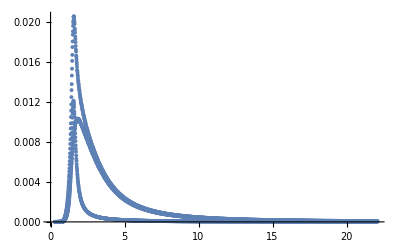

```mathematica
PlotHST[{Fq4πfull, Fq4πa1, Fq4πb1}, PlotRange->All]
```

## File

```mathematica
SetDirectory[NotebookDirectory[]];
<<"wang_data.m";
decays={#["in"],#["out"]}&/@Normal[DeleteDuplicates[dsFF[All,{"in","out"}]]];
Clear[$FF];
$FF[data_]:=Module[{},Switch[data["func"],"FF",Return[data["F0"]/(1-m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];,"GG",Return[data["F0"]/(1+m232/data["mFit"]^2+data["delta"] (m232/data["mFit"]^2)^2)];];];
(*Clear[cS,cA];*)
Clear[FF];
FF[query_]:=Module[{$res},$res=dsFF[query];
Return[cS $FF[$res[1]]+cA $FF[$res[2]]]];
```

## Main calculation

```mathematica
result={};
AppendTo[result,{"in","out","Vckm","l nul","pi" ,"rho","2pi", "3pi", "a1->4pi","a1+b1->4pi", "5pi"}];
i=.0;
PrintTemporary[Dynamic[dec],"Завершено",Dynamic[Floor[i/36*100,-0.1]], "%" ];
Do[
{in,out}=dec;
i=i+1;
Clear[m1,m2,quark1,quark2,f1,f2,g1,g2,Vckm,cS,cA];
m1=dsParticles[in]["mass"]; m2=dsParticles[out]["mass"];
cA=cA1[out,in];cS=cS1[out,in];
f1=FF[Select[#in==in&&#out==out&&#f=="f1"&]];
f2=FF[Select[#in==in&&#out==out&&#f=="f2"&]];
g1=FF[Select[#in==in&&#out==out&&#f=="g1"&]];
g2=FF[Select[#in==in&&#out==out&&#f=="g2"&]];
quark1=Characters[Quarks[in]];
quark2=Characters[Quarks[out]];
Vckm1=First[(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]])];
quarkrazn=(quark1[[1]]-quark2[[1]])+(quark1[[2]]-quark2[[2]])+(quark1[[3]]-quark2[[3]]);
Vckm2=-quarkrazn+Vckm1;
Vckm=V[Vckm1,Vckm2];
m3=0; m4=0;
Γl1=NIntegrate[dΓl, {m232,0,(m1-m2)^2}];
Γl2=NIntegrate[dΓl1,{m122,m12min,m12max},{m232,m23min,m23max}];
Γl0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["width"];
Brl=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\nu"]&]][[1]]["br"];
fullΓ=Γl0/Brl;
Hρ=HT/.{m232-> mρ^2};
Γρ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fρ^2*(1/(8*π))*Vckm^2*Hρ;
Hπ=HL/.{m232-> mπ^2};
Γπ=(Gf^2/2)*(1/(2*Y+1))*(1/(2*m1))*fπ^2*(1/(8*π))*Vckm^2*Hπ;
Ha1=HT/.{m232-> ma1^2};
Γρ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\rho"]&]][[1]]["width"];
Γπ0=dsWidths[Select[#in==in&&#out==out&&!StringFreeQ[#X,"\\pi"]&]][[1]]["width"];
Γ2π=NIntegrate[dΓ2π, {m232,4mπ^2,(m1-m2)^2}];
Γ3π=NIntegrate[dΓ3π, {m232,9mπ^2,(m1-m2)^2}];
Γ4πa1=NIntegrate[dΓ4πa1, {m232,16mπ^2,(m1-m2)^2}];
Γ4πfull=NIntegrate[dΓ4πfull, {m232,16mπ^2,(m1-m2)^2}];
Γ5π=NIntegrate[dΓ5π, {m232,25mπ^2,(m1-m2)^2}];
AppendTo[result,{in,out,Vckm1->Vckm2,Floor[Chop[Γl1/fullΓ],-0.000001]*100,Floor[Chop[Γπ/fullΓ],-0.0000000001]*100,Floor[Chop[Γρ/fullΓ],-0.00000001]*100,Floor[Chop[Γ2π/fullΓ],-0.0000001]*100,Floor[Chop[Γ3π/fullΓ],-0.0000001]*100,Floor[Chop[Γ4πa1/fullΓ],-0.0000001]*100,Floor[Chop[Γ4πfull/fullΓ],-0.0000001]*100,Floor[Chop[Γ5π/fullΓ],-0.0000001]*100}];
,{dec,decays}];
result
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.04309}. NIntegrate obtained TraditionalForm`6.199949246656747`*^-14 and TraditionalForm`2.7953540267495105`*^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`18 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m122, m232} = TraditionalForm`{0.468141, 0.0332227}. NIntegrate obtained TraditionalForm`6.200280512010538`*^-14 and TraditionalForm`5.231484967839733`*^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`m232 near TraditionalForm`{m232} = TraditionalForm`{0.0429364}. NIntegrate obtained TraditionalForm`6.139831083689381`*^-14 and TraditionalForm`2.321958443411979`*^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

(in | out | Vckm | l nul | pi | rho | 2pi | 3pi | a1->4pi | a1+b1->4pi | 5pi
\Xi_{cc}^{++} | \Lambda_{c}^{+} | c→d | 0.4936 | 0.377359 | 0.9932 | 0.86341 | 0.20795 | 0.03016 | 0.06371 | 0.00022
\Xi_{cc}^{++} | \Sigma_{c}^{+} | c→d | 0.4503 | 0.301942 | 1.04919 | 0.89963 | 0.15367 | 0.01008 | 0.01892 | 0.00004
\Xi_{cc}^{++} | \Xi_{c}^{+} | c→s | 4.9858 | 8.30163 | 12.3268 | 10.0496 | 0.63392 | 0.02525 | 0.04596 | 0.00006
\Xi_{cc}^{++} | \Xi_{c}^{\prime+} | c→s | 5.975 | 6.92904 | 17.6055 | 14.0915 | 0.7253 | 0.01716 | 0.03065 | 0.00003
\Xi_{cc}^{+} | \Sigma_{c}^{0} | c→d | 0.2988 | 0.201094 | 0.69752 | 0.5978 | 0.10132 | 0.00659 | 0.01236 | 0.00003
\Xi_{cc}^{+} | \Xi_{c}^{0} | c→s | 1.6513 | 2.74944 | 4.08255 | 3.32834 | 0.20995 | 0.00837 | 0.01522 | 0.00002
\Xi_{cc}^{+} | \Xi_{c}^{\prime0} | c→s | 1.984 | 2.30995 | 5.85562 | 4.68409 | 0.23845 | 0.0056 | 0.00999 | 0.00001
\Omega_{cc}^{+} | \Xi_{c}^{0} | c→d | 0.2079 | 0.293426 | 0.512133 | 0.42059 | 0.03418 | 0.00166 | 0.00306 | 0.00001
\Omega_{cc}^{+} | \Xi_{c}^{\prime0} | c→d | 0.2492 | 0.244044 | 0.710986 | 0.57731 | 0.03896 | 0.0011 | 0.00199 | 0.00001
\Omega_{cc}^{+} | \Omega_{c}^{0} | c→s | 6.6604 | 11.1885 | 22.5567 | 16.8782 | 0.26464 | 0.00357 | 0.00479 | 0.00001
\Xi_{bb}^{0} | \Sigma_{b}^{+} | b→u | 0.0043 | 1.43×10^-6 | 0.000434 | 0.00043 | 0.00038 | 0.00047 | 0.00058 | 0.00128
\Xi_{bb}^{0} | \Xi_{bc}^{+} | b→c | 2.5911 | 0.00347432 | 0.567736 | 0.54037 | 0.39867 | 0.39686 | 0.49937 | 0.11346
\Xi_{bb}^{0} | \Xi_{bc}^{\prime+} | b→c | 1.1503 | 0.00062621 | 0.12777 | 0.12499 | 0.11273 | 0.14148 | 0.17241 | 0.04995
\Xi_{bb}^{-} | \Lambda_{b}^{0} | b→u | 0.0011 | 8.3×10^-7 | 0.000223 | 0.00022 | 0.00017 | 0.00016 | 0.00021 | 0.00031
\Xi_{bb}^{-} | \Sigma_{b}^{0} | b→u | 0.0022 | 7.2×10^-7 | 0.000218 | 0.00022 | 0.00019 | 0.00024 | 0.00029 | 0.00065
\Xi_{bb}^{-} | \Xi_{bc}^{0} | b→c | 2.6207 | 0.00348729 | 0.571918 | 0.54437 | 0.40173 | 0.40023 | 0.50356 | 0.11458
\Xi_{bb}^{-} | \Xi_{bc}^{\prime0} | b→c | 1.1556 | 0.0006233 | 0.127653 | 0.12488 | 0.11266 | 0.14154 | 0.17246 | 0.05005
\Omega_{bb}^{-} | \Xi_{b}^{0} | b→u | 0.002 | 1.64×10^-6 | 0.000451 | 0.00044 | 0.00033 | 0.00032 | 0.00041 | 0.00047
\Omega_{bb}^{-} | \Xi_{b}^{\prime0} | b→u | 0.0044 | 1.44×10^-6 | 0.000453 | 0.00045 | 0.0004 | 0.00049 | 0.0006 | 0.00134
\Omega_{bb}^{-} | \Omega_{bc}^{0} | b→c | 4.8074 | 0.00702028 | 1.13376 | 1.07854 | 0.79206 | 0.77631 | 0.97902 | 0.21616
\Omega_{bb}^{-} | \Omega_{bc}^{\prime0} | b→c | 2.1266 | 0.00125917 | 0.256083 | 0.25058 | 0.22639 | 0.28019 | 0.34192 | 0.09663
\Xi_{bc}^{+} | \Lambda_{b}^{0} | c→d | 0.2234 | 0.0438203 | 0.486081 | 0.41499 | 0.07805 | 0.00879 | 0.01866 | 0.00005
\Xi_{bc}^{+} | \Sigma_{b}^{0} | c→d | 0.1483 | 0.0305532 | 0.402743 | 0.33162 | 0.02915 | 0.00103 | 0.00188 | 0.00001
\Xi_{bc}^{+} | \Xi_{b}^{0} | c→s | 2.3 | 0.927201 | 5.83855 | 4.71893 | 0.24847 | 0.00837 | 0.01512 | 0.00002
\Xi_{bc}^{0} | \Sigma_{b}^{-} | c→d | 0.1121 | 0.0232861 | 0.305524 | 0.25129 | 0.02167 | 0.00075 | 0.00137 | 0.00001
\Xi_{bc}^{0} | \Xi_{b}^{-} | c→s | 0.8684 | 0.352921 | 2.20629 | 1.78221 | 0.09218 | 0.00306 | 0.00552 | 0.00001
\Omega_{bc}^{0} | \Xi_{b}^{-} | c→d | 0.2542 | 0.0383789 | 0.511148 | 0.44309 | 0.1046 | 0.01482 | 0.03128 | 0.00011
\Omega_{bc}^{0} | \Omega_{b}^{-} | c→s | 6.0272 | 1.25182 | 16.6045 | 13.588 | 1.06522 | 0.03442 | 0.06279 | 0.00007
\Xi_{bc}^{+} | \Sigma_{c}^{++} | b→u | 0.0035 | 2.63×10^-6 | 0.000237 | 0.00024 | 0.00021 | 0.00027 | 0.00033 | 0.0016
\Xi_{bc}^{+} | \Xi_{cc}^{++} | b→c | 1.5843 | 0.00802878 | 0.437755 | 0.41395 | 0.28927 | 0.26757 | 0.34057 | 0.07028
\Xi_{bc}^{0} | \Lambda_{c}^{+} | b→u | 0.0003 | 5.1×10^-7 | 0.000043 | 0.00005 | 0.00004 | 0.00004 | 0.00004 | 0.00016
\Xi_{bc}^{0} | \Sigma_{c}^{+} | b→u | 0.0007 | 5.×10^-7 | 0.000046 | 0.00005 | 0.00004 | 0.00006 | 0.00007 | 0.00031
\Xi_{bc}^{0} | \Xi_{cc}^{+} | b→c | 0.6027 | 0.00305399 | 0.166513 | 0.15746 | 0.11004 | 0.10178 | 0.12955 | 0.02674
\Omega_{bc}^{0} | \Xi_{c}^{+} | b→u | 0.0005 | 9.4×10^-7 | 0.000088 | 0.00009 | 0.00007 | 0.00007 | 0.00009 | 0.00026
\Omega_{bc}^{0} | \Omega_{cc}^{+} | b→c | 1.8684 | 0.00663499 | 0.429286 | 0.40678 | 0.28946 | 0.27921 | 0.35315 | 0.07842)

## Make tex tables

```mathematica
dec1=Select[result,!StringFreeQ[#[[1]],"{cc}"]&];
dec2=Select[result,!StringFreeQ[#[[1]],"{bc}"]&];
dec3=Select[result,!StringFreeQ[#[[1]],"{bb}"]&];
```

```mathematica
toString[a_]:=If[Abs[a]<10^-3,ToString[ScientificForm[a,3],TeXForm],ToString[NumberForm[a,3]]];
makestr[dec_]:=Module[{str,qwert,in,out,Brlnul,Brπ,Brρ,Br2π,Br3π,Br4πa1,Br4πfull,Br5π},str="\\begin{tabular}{|l|c|c|c|c|c|c|}\n";
str=str<>"\\hline \n";
str=str<>"\\multirow{2}{*}{$\\B_1\\to\ \\B_2$}& \\multicolumn{6}{c|}{Modes}"<>"\\\\"<>"\n";
str=str<>"\\cline{2-7}"<>"\n";
str=str<>"& $l\\nu_l$ & $\\pi$ & $\\rho$ & $2\\pi$ & $3\\pi$ &   $5\\pi$"<>"\\\\"<>"\n";
str=str<>"\\hline \n";
str=str<>"\\hline \n";
Do[{in,out,Brlnul,Brπ,Brρ,Br2π,Br3π,Bra1,Br4π,Br5π}=qwert;
str=str<>"$"<>in<>"\\to\ "<>out<>"$&$"<>toString[Brlnul]<>"$&$"<>toString[Brπ]<>"$&$"<>toString[Brρ]<>"$&$"<>toString[Br2π]<>"$&$"<>toString[Br3π]<>"$&$"<>toString[Br5π]<>"$\\\\"<>"\n";
str=str<>"\\hline \n";,{qwert,dec}];
str=str<>"\\end{tabular}\n";
Return[str];]
```

```mathematica
str1=makestr[dec1];
str2=makestr[dec2];
str3=makestr[dec3];
```

Set::shape: Lists TraditionalForm`{in$1083646, out$1083646, Brlnul$1083646, Brπ$1083646, Brρ$1083646, Br2π$1083646, Br3π$1083646, Bra1$1083646, Br4π$1083646, Br5π$1083646} and TraditionalForm`{"\\Xi_{cc}^{++}", "\\Lambda_{c}^{+}", "c" → "d", 0.4936, 0.377359, 0.9932, 0.86341, 0.20795, 0.03016, 0.06371, 0.00022} are not the same shape.

StringJoin::string: String expected at position TraditionalForm`2 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`4 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`6 in TraditionalForm`« 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Set::shape: Lists TraditionalForm`{in$1083646, out$1083646, Brlnul$1083646, Brπ$1083646, Brρ$1083646, Br2π$1083646, Br3π$1083646, Bra1$1083646, Br4π$1083646, Br5π$1083646} and TraditionalForm`{"\\Xi_{cc}^{++}", "\\Sigma_{c}^{+}", "c" → "d", 0.4503, 0.301942, 1.04919, 0.89963, 0.15367, 0.01008, 0.01892, 0.00004} are not the same shape.

Set::shape: Lists TraditionalForm`{in$1083646, out$1083646, Brlnul$1083646, Brπ$1083646, Brρ$1083646, Br2π$1083646, Br3π$1083646, Bra1$1083646, Br4π$1083646, Br5π$1083646} and TraditionalForm`{"\\Xi_{cc}^{++}", "\\Xi_{c}^{+}", "c" → "s", 4.9858, 8.30163, 12.3268, 10.0496, 0.63392, 0.02525, 0.04596, 0.00006} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Set::shape: Lists TraditionalForm`{in$1085679, out$1085679, Brlnul$1085679, Brπ$1085679, Brρ$1085679, Br2π$1085679, Br3π$1085679, Bra1$1085679, Br4π$1085679, Br5π$1085679} and TraditionalForm`{"\\Xi_{bc}^{+}", "\\Lambda_{b}^{0}", "c" → "d", 0.2234, 0.0438203, 0.486081, 0.41499, 0.07805, 0.00879, 0.01866, 0.00005} are not the same shape.

StringJoin::string: String expected at position TraditionalForm`2 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`4 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`6 in TraditionalForm`« 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Set::shape: Lists TraditionalForm`{in$1085679, out$1085679, Brlnul$1085679, Brπ$1085679, Brρ$1085679, Br2π$1085679, Br3π$1085679, Bra1$1085679, Br4π$1085679, Br5π$1085679} and TraditionalForm`{"\\Xi_{bc}^{+}", "\\Sigma_{b}^{0}", "c" → "d", 0.1483, 0.0305532, 0.402743, 0.33162, 0.02915, 0.00103, 0.00188, 0.00001} are not the same shape.

Set::shape: Lists TraditionalForm`{in$1085679, out$1085679, Brlnul$1085679, Brπ$1085679, Brρ$1085679, Br2π$1085679, Br3π$1085679, Bra1$1085679, Br4π$1085679, Br5π$1085679} and TraditionalForm`{"\\Xi_{bc}^{+}", "\\Xi_{b}^{0}", "c" → "s", 2.3, 0.927201, 5.83855, 4.71893, 0.24847, 0.00837, 0.01512, 0.00002} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

Set::shape: Lists TraditionalForm`{in$1087707, out$1087707, Brlnul$1087707, Brπ$1087707, Brρ$1087707, Br2π$1087707, Br3π$1087707, Bra1$1087707, Br4π$1087707, Br5π$1087707} and TraditionalForm`{"\\Xi_{bb}^{0}", "\\Sigma_{b}^{+}", "b" → "u", 0.0043, 1.43×10^-6, 0.000434, 0.00043, 0.00038, 0.00047, 0.00058, 0.00128} are not the same shape.

StringJoin::string: String expected at position TraditionalForm`2 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`4 in TraditionalForm`« 1 ».

StringJoin::string: String expected at position TraditionalForm`6 in TraditionalForm`« 1 ».

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

Set::shape: Lists TraditionalForm`{in$1087707, out$1087707, Brlnul$1087707, Brπ$1087707, Brρ$1087707, Br2π$1087707, Br3π$1087707, Bra1$1087707, Br4π$1087707, Br5π$1087707} and TraditionalForm`{"\\Xi_{bb}^{0}", "\\Xi_{bc}^{+}", "b" → "c", 2.5911, 0.00347432, 0.567736, 0.54037, 0.39867, 0.39686, 0.49937, 0.11346} are not the same shape.

Set::shape: Lists TraditionalForm`{in$1087707, out$1087707, Brlnul$1087707, Brπ$1087707, Brρ$1087707, Br2π$1087707, Br3π$1087707, Bra1$1087707, Br4π$1087707, Br5π$1087707} and TraditionalForm`{"\\Xi_{bb}^{0}", "\\Xi_{bc}^{\\prime+}", "b" → "c", 1.1503, 0.00062621, 0.12777, 0.12499, 0.11273, 0.14148, 0.17241, 0.04995} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

```mathematica
DeleteFile["table11.tex"];
DeleteFile["table22.tex"];
DeleteFile["table33.tex"];
WriteString["table11.tex",str1];
WriteString["table22.tex",str2];
WriteString["table33.tex",str3];
Close["table11.tex"];
Close["table22.tex"];
Close["table33.tex"];
```

## Make pictures

### Spectral functions

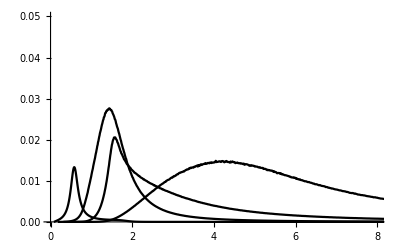

```mathematica
Show[PlotHST[Fq2π/10,Joined-> True,PlotStyle-> Black, PlotRange->{{0,8},{0,0.05}}, ShowErrors-> False],PlotHST[Fq3π,Joined-> True,PlotStyle-> Black, PlotRange->{{0,8},{0,0.05}}, ShowErrors-> False],PlotHST[Fq4πfull,Joined-> True,PlotStyle-> Black, PlotRange->{{0,8},{0,0.05}}, ShowErrors-> False],PlotHST[10*Fq5π,Joined-> True,PlotStyle-> Black, PlotRange->{{0,8},{0,0.05}}, ShowErrors-> False]]
```

### 3pi 5pi